# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z)+C sin^(2k)(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1∧a^2=b^2

Domain Map

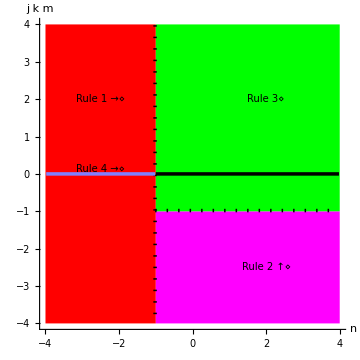

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

Rule a:  ∫(A+B Csc[c+d x]+C Csc[c+d x]^2)/(a+b Csc[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z+C z^2)/(a+b z)=A/a-(z(b A-a B-a C z))/(a(a+b z))

#### Note: The rule for integrands of the same form when a^2-b^2≠0 could subsume this rule, but the resulting antiderivative will look less like the integrand involving sines instead of cosecants.

#### Rule a: If a^2-b^2=0, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2)/(a+b Csc[c+d x])ⅆx  ⟶  (A x)/a+C/b∫Csc[c+d x]ⅆx-(b A-a B+b C)/a∫Csc[c+d x]/(a+b Csc[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a + 
  C/b*Int[sin[c+d*x]^(-1),x] - 
  (b*A-a*B+b*C)/a*Int[sin[c+d*x]^(-1)/(a+b*sin[c+d*x]^(-1)),x] /;
FreeQ[{a,b,c,d,A,B,C},x] && ZeroQ[a^2-b^2]
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^(-2))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a + C/b*Int[sin[c+d*x]^(-1),x] - 
  (b*A+b*C)/a*Int[sin[c+d*x]^(-1)/(a+b*sin[c+d*x]^(-1)),x] /;
FreeQ[{a,b,c,d,A,C},x] && ZeroQ[a^2-b^2]
```

Rule b:  ∫(A+B Csc[c+d x]+C Csc[c+d x]^2)/(√(a+b Csc[c+d x]))ⅆx

#### Derivation: Rule 3 with m=0, k=-1 and n=-1/2

#### Rule b: If a^2-b^2=0, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2)/(√(a+b Csc[c+d x]))ⅆx  ⟶  -(2 C Cot[c+d x])/(d √(a+b Csc[c+d x]))+1/a∫(a A+(a B-b C) Csc[c+d x])/(√(a+b Csc[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*C*Cot[c+d*x]/(d*Sqrt[a+b*Csc[c + d*x]]) + 
  Dist[1/a,Int[Sim[a*A+(a*B-b*C)*sin[c+d*x]^(-1),x]/Sqrt[a+b*sin[c+d*x]^(-1)],x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && ZeroQ[a^2-b^2]
```

```mathematica
Int[(A_+C_.*sin[c_.+d_.*x_]^(-2))/Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*C*Cot[c+d*x]/(d*Sqrt[a+b*Csc[c + d*x]]) + 
  Dist[1/a,Int[Sim[a*A-b*C*sin[c+d*x]^(-1),x]/Sqrt[a+b*sin[c+d*x]^(-1)],x]] /;
FreeQ[{a,b,c,d,A,C},x] && ZeroQ[a^2-b^2]
```

Rule c:  ∫((Sin[c+d x]^j)^(m/2)(A+B Csc[c+d x]+C Csc[c+d x]^2))/(√(a+b Csc[c+d x]))ⅆx

#### Derivation: Rule 2 with j m=1/2, k=-1 and n=-1/2

#### Rule c: If j^2=1 ∧ a^2-b^2=0 ∧ j m=1/2, then

∫((Sin[c+d x]^j)^(m/2)(A+B Csc[c+d x]+C Csc[c+d x]^2))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
-(2A Cos[c+d x])/(d(Sin[c+d x]^j)^(m/2)√(a+b Csc[c+d x]))-1/a∫(b A-a B-a C Csc[c+d x])/((Sin[c+d x]^j)^(m/2)√(a+b Csc[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))/
    Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*A*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) - 
  Dist[1/a,
    Int[Sim[b*A-a*B-a*C*sin[c+d*x]^(-1),x]/((sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^(-1)]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+C_.*sin[c_.+d_.*x_]^(-2))/Sqrt[a_.+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*A*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) - 
  Dist[1/a,
    Int[Sim[b*A-a*C*sin[c+d*x]^(-1),x]/((sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^(-1)]),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2
```

Rule 4:  ∫(A+B Sin[c+d x]^k+C Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Recurrence 7 with j m=0 and k=1 plus recurrence 7 with A=0, B=C and j m=k

#### Rule 4a: If a^2-b^2=0 ∧ n<-1, then

∫(A+B Sin[c+d x]+C Sin[c+d x]^2) (a+b Sin[c+d x])^n ⅆx  ⟶  
((b (A+C)-a B) Cos[c+d x](a+b Sin[c+d x])^n)/(a d (2n+1))+
1/(a^2(2n+1))∫(a A(n+1)+n(b B-a C)+b C (2n+1)Sin[c+d x])(a+b Sin[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]+C_.*sin[c_.+d_.*x_]^2)*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  (b*(A+C)-a*B)*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(a*d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[Sim[a*A*(n+1)+n*(b*B-a*C)+b*C*(2*n+1)*sin[c+d*x],x]*(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^2)*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  b*(A+C)*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(a*d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[Sim[a*A*(n+1)-a*C*n+b*C*(2*n+1)*sin[c+d*x],x]*(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 1 with m=0 and k=-1

#### Rule 4b: If a^2-b^2=0 ∧ n<-1, then

∫(A+B Csc[c+d x]+C Csc[c+d x]^2) (a+b Csc[c+d x])^n ⅆx  ⟶  
((a B-b(A+C))Cot[c+d x](a+b Csc[c+d x])^n)/(b d (2n+1))+
1/(a^2 (2n+1))∫(a A(2 n+1)+(b C n-(b A-a B)(n+1))Csc[c+d x])(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1)+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  (a*B-b*(A+C))*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(b*d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[Sim[a*A*(2*n+1)+(b*C*n-(b*A-a*B)*(n+1))*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

```mathematica
Int[(A_.+C_.*sin[c_.+d_.*x_]^(-2))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -(A+C)*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[Sim[a*A*(2*n+1)+(b*C*n-b*A*(n+1))*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

Rules 1-3:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Rule: If j^2=k^2=1 ∧ a^2-b^2=0, then

∫(Sin[c+d x]^j)^m(B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶
∫(Sin[c+d x]^j)^(m+j k)(B+C Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  Int[(sin[c+d*x]^j)^(m+j*k)*(B+C*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^n,x] /;
FreeQ[{a,b,c,d,B,C,m,n},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2]
```

#### Derivation: Recurrence 12 plus recurrence 7 with A=0, B=C and m=m+j k

#### Rule 1: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
((a B-b A-b C)Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(b d (2n+1))+
1/(a^2 (2n+1))∫(Sin[c+d x]^j)^m·
(a A(2 n+1)-(b B-a A-a C)(j k m+(k+1)/2)+(b C n-(b A-a B)(n+1)+(a B-b A-b C)(j k m+(k+1)/2))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  (a*B-b*A-b*C)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(2*n+1)-(b*B-a*A-a*C)*(j*k*m+(k+1)/2)+
        (b*C*n-(b*A-a*B)*(n+1)+(a*B-b*A-b*C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && n≤-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(A+C)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(2*n+1)+a*(A+C)*(j*k*m+(k+1)/2)+
        (b*C*n-b*A*(n+1)-b*(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && n≤-1
```

#### Derivation: Recurrence 11 with B=0

#### Rule 2: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m<-1 ∧ n>-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+1/(a(j k m+(k+1)/2))∫(Sin[c+d x]^j)^(m+j k)·
(a B(j k m+(k+1)/2)-b A n+a(A(n+1)+(A+C)(j k m+(k+1)/2))Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*B*(j*k*m+(k+1)/2)-b*A*n+a*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m<-1 && n>-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[-b*A*n+a*(A*(n+1)+(A+C)*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && j*k*m<-1 && n>-1
```

#### Derivation: Recurrence 8 with A=0, B=C and m=m+j k

#### Rule 3: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k+3)/2≠0 ∧ j k m≥-1 ∧ n>-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k+C Sin[c+d x]^(2k)) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(C Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(d (j k m+n+(k+3)/2))+1/(a (j k m+n+(k+3)/2))∫(Sin[c+d x]^j)^m·
(a A (n+1)+a(A+C)(j k m+(k+1)/2)+(b C n+a B (j k m+n+(k+3)/2)) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+B_.*sin[c_.+d_.*x_]^k_.+C_.*sin[c_.+d_.*x_]^k2_)*
    (a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k+3)/2)) + 
  Dist[1/(a*(j*k*m+n+(k+3)/2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(n+1)+a*(A+C)*(j*k*m+(k+1)/2)+(b*C*n+a*B*(j*k*m+n+(k+3)/2))*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && NonzeroQ[j*k*m+n+(k+3)/2] && j*k*m≥-1 && n>-1
```

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+C_.*sin[c_.+d_.*x_]^k2_)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -C*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k+3)/2)) + 
  Dist[1/(a*(j*k*m+n+(k+3)/2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(n+1)+a*(A+C)*(j*k*m+(k+1)/2)+b*C*n*sin[c+d*x]^k,x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && OneQ[j^2,k^2] && k2===2*k && ZeroQ[a^2-b^2] && 
  RationalQ[m,n] && NonzeroQ[j*k*m+n+(k+3)/2] && j*k*m≥-1 && n>-1
```